```mathematica
D[x^3+6x,{x,2}]
```

```mathematica
6 g[y]
clear[x]
```

6 g[y]

```mathematica
clear[g[y]]
D[x^3+6x,{x,2}]
```

clear[g[y]]

6 g[y]

```mathematica
Clear["Global`*"]
```

```mathematica
D[x^3+6x,{x,2}]
```

```mathematica
6 x
```

6 x

```mathematica
x=φ[y];
```

```mathematica
z=f[x,y];
```

```mathematica
D[z,{x,2}]
```

```mathematica
Derivative[2,0][f][φ[y],y]
Dt[z,{x,2}]
```

f^(2,0)[φ[y],y]

Dt[y,{φ[y],2}] f^(0,1)[φ[y],y]+Dt[y,φ[y]] f^(1,1)[φ[y],y]+Dt[y,φ[y]] (Dt[y,φ[y]] f^(0,2)[φ[y],y]+f^(1,1)[φ[y],y])+f^(2,0)[φ[y],y]

```mathematica
Dt[z,{x,2}]
```

Dt[y,{φ[y],2}] f^(0,1)[φ[y],y]+Dt[y,φ[y]] f^(1,1)[φ[y],y]+Dt[y,φ[y]] (Dt[y,φ[y]] f^(0,2)[φ[y],y]+f^(1,1)[φ[y],y])+f^(2,0)[φ[y],y]

```mathematica
Dt[z,x]
```

Dt[y,φ[y]] f^(0,1)[φ[y],y]+f^(1,0)[φ[y],y]

```mathematica
Dt[z,{x,2}]
```

Dt[y,{φ[y],2}] f^(0,1)[φ[y],y]+Dt[y,φ[y]] f^(1,1)[φ[y],y]+Dt[y,φ[y]] (Dt[y,φ[y]] f^(0,2)[φ[y],y]+f^(1,1)[φ[y],y])+f^(2,0)[φ[y],y]

```mathematica
Dt[z,{x,2}];Simplify[%]
```

Dt[y,{φ[y],2}] f^(0,1)[φ[y],y]+Dt[y,φ[y]]^2 f^(0,2)[φ[y],y]+2 Dt[y,φ[y]] f^(1,1)[φ[y],y]+f^(2,0)[φ[y],y]

```mathematica
z
```

f[φ[y],y]

```mathematica
clc
```

clc

```mathematica
clear
```

clear

```mathematica
Information[clear]
```

```mathematica
clear all
```

all clear

```mathematica
reset
```

reset

```mathematica
x
```

φ[y]

```mathematica
Dt[y,{φ[y],2}]
```

Dt[y,{φ[y],2}]

```mathematica
Simplify[Dt[y,{φ[y],2}]];
```

```mathematica
Dt[y,{φ[y],2}]
```

Dt[y,{φ[y],2}]

```mathematica
D[Integrate[e^yf[x-t],{t,0,y}],x]
```

∫_0^y e^yf[-t+φ[y]] Log[e] yf'[-t+φ[y]]ⅆt

```mathematica
D[Integrate[e^{y}f[x-t],{t,0,y}],x]
```

```mathematica
{∫_0^y e^y f'[-t+φ[y]]ⅆt}
Clear["Global`*"]
```

{∫_0^y e^y f'[-t+φ[y]]ⅆt}

```mathematica
Clear["Global`*"]
```

```mathematica
D[Integrate[e^{y}f[x-t],{t,0,y}],x]
```

{∫_0^y e^y f'[-t+x]ⅆt}

```mathematica
c=D[Integrate[e^{y}f[x-t],{t,0,y}],x]
```

{∫_0^y e^y f'[-t+x]ⅆt}

```mathematica
D[c,y]
```

{∫_0^y e^y Log[e] f'[-t+x]ⅆt+e^y f'[x-y]}

```mathematica
D[x y-Exp[x]+Exp[y]==0,x,NonConstants->y]
```

-ⅇ^x+y+ⅇ^y D[y,x,NonConstants→{y}]+x D[y,x,NonConstants→{y}]==0

```mathematica
FindInstance[-ⅇ^x+y+ⅇ^y D[y,x,NonConstants->{y}]+x D[y,x,NonConstants->{y}]==0,{x,y}]
```

FindInstance::exvar: 系统包含与变量 {x,y} 无关的非常量表达式 NonConstants.

FindInstance[-ⅇ^x+y+ⅇ^y D[y,x,NonConstants→{y}]+x D[y,x,NonConstants→{y}]==0,{x,y}]

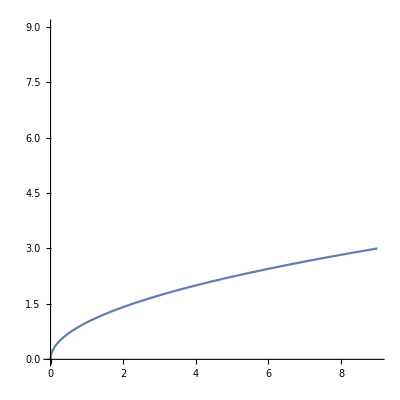

```mathematica
Plot[x^{1/2},{x,0,9},AxesOrigin->{0,0},AspectRatio->1,PlotRange->{{0,9},{0,9}}]
```

```mathematica
sqrt[11]/2-3/sqrt[5]
```

-3/sqrt[5]+sqrt[11]/2

```mathematica
Sqrt[11]/2-3/Sqrt[5]
```

-3/(√5)+(√11)/2

```mathematica
N[-3/(√5)+(√11)/2,3]
```

0.317

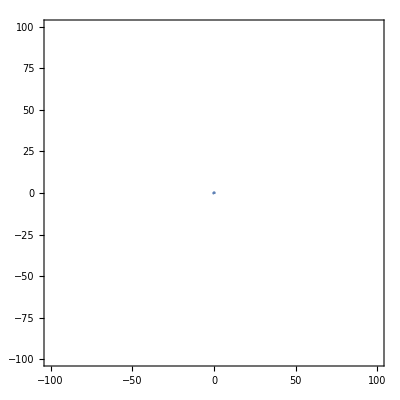

```mathematica
ContourPlot[3 x^2+3y^2-2x y-1==0,{x,-100,100},{y,-100,100}]
```